```mathematica
#3 Cellular Automata- From Classical Computation to Quantum Error Correction #3
```

This project reinterprets Conway Game of Life (GPU-only) not as a mere visualization tool, but as a “code-as-proof” model for creating a deterministic, self-organizing representation from a causal seed, mirroring the core tenets of the Daedaelus philosophy. Here, the cryptographic hash of an input serves as the initial, conserved quantity of information. This seed is not broadcast to a global controller; instead, it provides the local rules for a computational fabric—a cellular automaton—that evolves based on “local information”.

```mathematica
Quiet@Unprotect[Ex,ExportIfNotExists,path,BasicImageResolution,ImageSizeCentimetre,DefaultColours,PlotOptions,Embolden,Italicise];
ClearAll[Ex,ExportIfNotExists,path,BasicImageResolution,ImageSizeCentimetre,DefaultColours,PlotOptions,Embolden,Italicise];
SetAttributes[path,HoldFirst];
path[file_String]:=file;               
SetAttributes[Ex,HoldFirst];
Ex[dest_String,opts:OptionsPattern[Export]]:=(Print[#];#)&;                       
SetAttributes[ExportIfNotExists,HoldAll];
ExportIfNotExists[dest_String,expr_,opts:OptionsPattern[Export]]:=Print[expr];                           
Protect[path,Ex,ExportIfNotExists];
BasicImageResolution=72;
ImageSizeCentimetre=72/2.54;
DefaultColours=ColorData[97,"ColorList"];
PlotOptions[Axes]={AxesLabel->Style[{"x","y"},Italic],LabelStyle->Directive[Black,16]};
PlotOptions[Frame]=Join[PlotOptions[Axes],{Frame->True,RotateLabel->False}];
Embolden[s_]:=Style[s,Bold];SetAttributes[Embolden,Listable];
Italicise[s_]:=Style[s,Italic];SetAttributes[Italicise,Listable];
```

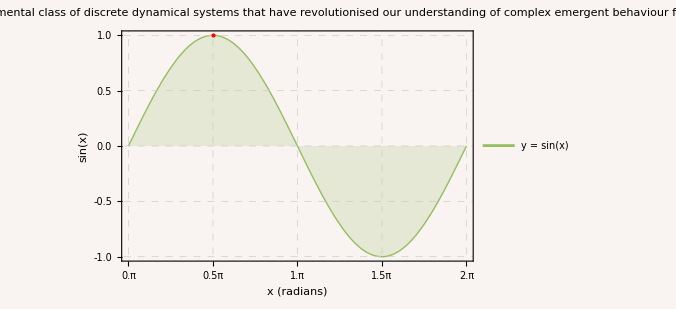

```mathematica
longText="✨ Cellular automata represent a fundamental class of discrete dynamical systems that have revolutionised our understanding of complex emergent behaviour from simple local rules. ✨";
demoFancy=Plot[Sin[x],{x,0,2 Pi},PlotStyle->Directive[Thick,ColorData["Rainbow"][0.55]],PlotRangePadding->Scaled[0.02],Frame->True,FrameStyle->Directive[Black,14,Thick],FrameLabel->{Style["x (radians)",Italic,14],Style["sin(x)",Italic,14]},FrameTicks->{{{#,Style[NumberForm[#,{3,1}],12]}&/@Range[-1,1,0.5],None},{{#,Style[ToString@TraditionalForm[#/Pi]<>"π",12]}&/@(Pi Range[0,2,0.5]),None}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[.8],Dashed],Background->Lighter[Blend[{White,ColorData["SolarColors"][.05]}],.9],Filling->Axis,FillingStyle->Directive[Opacity[.2],ColorData["Rainbow"][0.55]],PlotLabel->Pane[Style[longText,Bold,12,ColorData["Rainbow"][0.55]],ImageSize->{380,Automatic},Alignment->Center],PlotLegends->Placed[{Style["y = sin(x)",Italic,12]},{Right,Center}],Epilog->{Red,PointSize[Large],Point[{Pi/2,1}],Text[Style["peak",Bold,Red,12],{Pi/2,1.1}]},ImageSize->500];
demoFancy
```

```mathematica
ClearAll[f,evolve,seed,A]
f[x_,y_]:=Boole[y==3||(x==1&&y==2)];   
evolve[m_?MatrixQ]:=Module[{nbr=ListCorrelate[{{1,1,1},{1,0,1},{1,1,1}},m,2,0]},MapThread[f,{m,nbr},2]]
seed[{h_Integer,w_Integer}]:=Module[{m=ConstantArray[0,{h,w}],gun,offset},gun={{5,2},{5,3},{6,2},{6,3},{5,12},{6,12},{7,12},{4,13},{8,13},{3,14},{9,14},{3,15},{9,15},{6,16},{4,17},{8,17},{5,18},{6,18},{7,18},{6,19},{3,22},{4,22},{5,22},{3,23},{4,23},{5,23},{2,24},{6,24},{1,26},{2,26},{6,26},{7,26},{3,36},{4,36},{3,37},{4,37}};
offset={Ceiling[h/2]-10,Ceiling[w/2]-20};Scan[(m[[Sequence@@(#+offset)]]=1)&,gun];
m]
{height,width}={40,80};
A[0]=seed[{height,width}];
A[n_Integer?Positive]:=A[n]=evolve[A[n-1]];
Animate[ArrayPlot[A[t],PixelConstrained->8,ColorRules->{0->White,1->Black},Frame->False,ImageSize->Large],{t,0,200,1},AnimationRunning->False,AnimationRate->20,AnimationRepetitions->Infinity]
```

```mathematica
ClearAll[colorByAge]
colorByAge[0]:=RGBColor[1,1,1];
colorByAge[n_Integer?Positive]:=ColorData["Rainbow"][Rescale[Min[n,20],{1,20}]];
SetOptions[MatrixPlot,ColorFunction->colorByAge,ColorFunctionScaling->False,Frame->False,ImageSize->400];
ClearAll[initializeGrid]
initializeGrid[rows_Integer?Positive,columns_Integer?Positive,stat_?NumericQ]:=RandomChoice[{stat,1-stat}->{1,0},{rows,columns}];
ClearAll[updateCell]
updateCell[grid_,row_,col_]:=Module[{rmax=Length[grid],cmax=Length[First[grid]],state,nn,zeros},state=grid⟦row,col⟧;nn=Flatten[Table[grid⟦Mod[row+dr-1,rmax,1],Mod[col+dc-1,cmax,1]⟧,{dr,-1,1},{dc,-1,1}]];zeros=Count[nn,0]-Boole[state==0];Which[zeros<5||zeros≥7,0,zeros==5,state+1,zeros==6&&state>0,state+1,True,0]];
ClearAll[updateGrid]
updateGrid[grid_?MatrixQ]:=MapIndexed[updateCell[grid,##2⟦1⟧,##2⟦2⟧]&,grid,{2}];
ClearAll[runSimulation]
runSimulation[startGrid_,steps_Integer?Positive]:=Module[{grids={startGrid}},Do[AppendTo[grids,updateGrid[Last[grids]]];If[grids⟦-1⟧===grids⟦-2⟧,Break[]],{steps-1}];grids];
ClearAll[animateSimulation]
animateSimulation[grids_,fps_:6]:=ListAnimate[MatrixPlot/@grids,DefaultDuration->Length[grids]/fps];
SeedRandom[123];
initial=initializeGrid[200,200,0.25];
evolution=runSimulation[initial,100];
animateSimulation[evolution,8]
```